# MatrixRank

## Basic Examples

Find the number of linearly independent rows:

```mathematica
MatrixRank[{{1,2,3},{4,5,6},{7,8,9}}]
```

2

## Options

### Modulus

The rank of a matrix depends on the modulus used:

```mathematica
m={{1,0,4},{2,0,3},{2,1,2}};
```

With ordinary arithmetic, m  has the full rank of 3:

```mathematica
MatrixRank[m]
```

3

With arithmetic modulo 5, the rank is only 2:

```mathematica
MatrixRank[m,Modulus->5]
```

2

### Tolerance

The setting of Tolerance can affect the estimated rank for numerical ill-conditioned matrices:

```mathematica
m={{1,1,1},{0,10^-12,0},{0,0,10^-20}};
```

In exact arithmetic, m has full rank:

```mathematica
MatrixRank[m]
```

3

With machine arithmetic, the default is to consider elements that are too small as zero:

```mathematica
MatrixRank[N[m]]
```

2

With zero tolerance, even small terms may be taken into account:

```mathematica
MatrixRank[N[m],Tolerance->0]
```

3

With a tolerance greater than the pivot in the middle row, the last two rows are considered zero:

```mathematica
MatrixRank[N[m],Tolerance->10^(-8)]
```

1

## Applications

Most but not all random 10x10 0-1 matrices have full rank:

```mathematica
Table[MatrixRank[RandomInteger[1,{10,10}]],{20}]
```

{9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,9,10,9}

Estimate the average rank of a random 10x10 0-1 matrix:

```mathematica
Block[{n=10000},N[Sum[MatrixRank[RandomInteger[1,{10,10}]],{n}]/n]]
```

9.6883

Find the ranks of coprimality arrays:

```mathematica
m=Table[If[CoprimeQ[x,y],1,0],{x,20},{y,20}]
```

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0},{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1},{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0},{1,1,1,1,0,1,1,1,1,0,1,1,1,1,0,1,1,1,1,0},{1,0,0,0,1,0,1,0,0,0,1,0,1,0,0,0,1,0,1,0},{1,1,1,1,1,1,0,1,1,1,1,1,1,0,1,1,1,1,1,1},{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0},{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1},{1,0,1,0,0,0,1,0,1,0,1,0,1,0,0,0,1,0,1,0},{1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1},{1,0,0,0,1,0,1,0,0,0,1,0,1,0,0,0,1,0,1,0},{1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1},{1,0,1,0,1,0,0,0,1,0,1,0,1,0,1,0,1,0,1,0},{1,1,0,1,0,0,1,1,0,0,1,0,1,1,0,1,1,0,1,0},{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1},{1,0,0,0,1,0,1,0,0,0,1,0,1,0,0,0,1,0,1,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1},{1,0,1,0,0,0,1,0,1,0,1,0,1,0,0,0,1,0,1,0}}

```mathematica
MatrixRank[m]
```

13

```mathematica
ArrayPlot[m]
```

-Graphics-

```mathematica
Table[MatrixRank[Table[If[CoprimeQ[x,y],1,0],{x,n},{y,n}]],{n,50}]
```

{1,2,3,3,4,5,6,6,6,7,8,8,9,10,11,11,12,12,13,13,14,15,16,16,16,17,17,17,18,19,20,20,21,22,23,23,24,25,26,26,27,28,29,29,29,30,31,31,31,31}

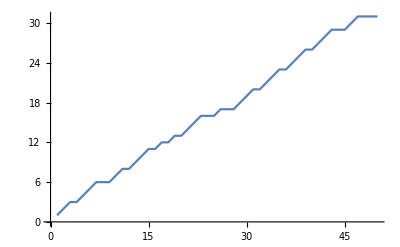

```mathematica
ListLinePlot[Table[MatrixRank[Table[If[CoprimeQ[x,y],1,0],{x,n},{y,n}]],{n,50}]]
```

## Properties & Relations

MatrixRank[m] is equal to Length[SingularValueList[m]]:

```mathematica
m=N[RandomInteger[1,{4,4}]];
```

```mathematica
SingularValueList[m]
```

{2.40651,1.41421,1.09941}

```mathematica
MatrixRank[m]==Length[SingularValueList[m]]
```

True

MatrixRank[m] plus the dimension of the null space is equal to the number of columns of m:

```mathematica
m=N[RandomInteger[1,{4,4}]];
```

```mathematica
{r,c}=Dimensions[m];
```

```mathematica
ns=NullSpace[m]
```

{{-0.707107,0.707107,-1.11022×10^-16,2.22045×10^-16}}

```mathematica
c==Length[ns]+MatrixRank[m]
```

True

The column and row rank of a matrix are equal:

```mathematica
m={{1,2,3},{4,5,6},{7,8,9}};
```

```mathematica
{MatrixRank[m],MatrixRank[Transpose[m]]}
```

{2,2}

The outer product of vectors has matrix rank 1:

```mathematica
v=RandomReal[1,1000];
```

```mathematica
MatrixRank[KroneckerProduct[v,v]]
```

1